```mathematica
sol[x_] = y[x] /. DSolve[ {y''[x] + 9 y[x]==0, y'[0]==1, y[0]==0},y[x],x]
```

{1/3 Sin[3 x]}

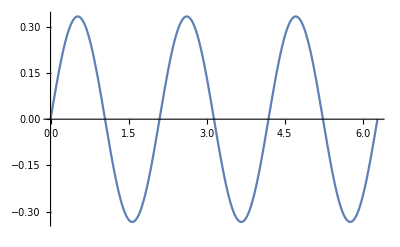

```mathematica
Plot[sol[z] , {z,0,2 Pi}]
```

```mathematica
//le condizioni al contorno costituiscono con l'eq differenziale un sistema di equazioni, il risultato è una regola di sostituzione, con in[1] ho già risolto valutando sol con la regola
```

```mathematica
DSolve[ {y''[x] + 9 y[x]==0, y'[0]==1, y[0]==0},y[x],x]
```

{{y[x]→1/3 Sin[3 x]}}

```mathematica
pippo pluto y[x] /. %
```

{1/3 pippo pluto Sin[3 x]}

```mathematica
f1[n_] = Normal[Series[Log[1+x] , {x,0,n}]]
```

Series::serlim: Series order specification n is not a machine-sized integer.

Log[1+x]

```mathematica
f1[4]
```

Log[1+x]

```mathematica
f2[n_] := Normal[Series[Log[1+x] , {x,0,n}]]
```

```mathematica
f2[4]
```

x-x^2/2+x^3/3-x^4/4

```mathematica
Solve[ a x^2 + b x + c == 0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
soleq2 = Solve[ a x^2 + b x + c == 0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
x /. soleq2
```

{(-b-√(b^2-4 a c))/(2 a),(-b+√(b^2-4 a c))/(2 a)}

```mathematica
x /. soleq2[[2]]
```

(-b+√(b^2-4 a c))/(2 a)

```mathematica
(*
\psi_{lm}(\theta\phi) viene fattorizzata in TH[th] PHI[phi] *)
```

```mathematica
eq2= -D[TH[th] PHI[phi] , {phi,2}] ==m^2 TH[th] PHI[phi];
sol2 = DSolve[ eq2 , PHI[phi], phi];
```

```mathematica
-TH[th] PHI''[phi]==m^2 PHI[phi] TH[th]
```

-TH[th] PHI''[phi]==m^2 PHI[phi] TH[th]

```mathematica
sol2
```

{{PHI[phi]→C[1] Cos[m phi]+C[2] Sin[m phi]}}

```mathematica
eq2= -D[TH[th] PHI[phi] , {phi,2}] ==m^2 TH[th] PHI[phi];
sol2 = DSolve[ eq2 , PHI[phi], phi];
sol2 = sol2 /. {C[1]->1 , C[2]->I};
```

```mathematica
sol2
```

{{PHI[phi]→Cos[m phi]+ⅈ Sin[m phi]}}

```mathematica
eq2= -D[TH[th] PHI[phi] , {phi,2}] ==m^2 TH[th] PHI[phi];
sol2 = DSolve[ eq2 , PHI[phi], phi];
sol2 = sol2 /. {C[1]->1 , C[2]->I};

eq1= -1/Sin[th] D[ Sin[th] D[ TH[th] PHI[phi], th] , th] - 1/Sin[th]^2 D[ TH[th] PHI[phi] , {phi,2}] == l(l+1) TH[th] PHI[phi];
```

```mathematica
eq1
```

-Csc[th]^2 TH[th] PHI''[phi]-Csc[th] (Cos[th] PHI[phi] TH'[th]+PHI[phi] Sin[th] TH''[th])==l (1+l) PHI[phi] TH[th]

```mathematica
Expand[%]
```

-Cot[th] PHI[phi] TH'[th]-Csc[th]^2 TH[th] PHI''[phi]-PHI[phi] TH''[th]==l PHI[phi] TH[th]+l^2 PHI[phi] TH[th]

```mathematica
Simplify[%]
```

Csc[th]^2 TH[th] PHI''[phi]+PHI[phi] (l (1+l) TH[th]+Cot[th] TH'[th]+TH''[th])==0

```mathematica
eq1 /. sol2
```

{-Csc[th]^2 TH[th] PHI''[phi]-Csc[th] (Cos[th] (Cos[m phi]+ⅈ Sin[m phi]) TH'[th]+(Cos[m phi]+ⅈ Sin[m phi]) Sin[th] TH''[th])==l (1+l) (Cos[m phi]+ⅈ Sin[m phi]) TH[th]}

```mathematica
sol2
```

{{PHI[phi]→Cos[m phi]+ⅈ Sin[m phi]}}

```mathematica
FullForm[ PHI''[phi]]
```

Derivative[2][PHI][phi]

```mathematica
eq2= -D[TH[th] PHI[phi] , {phi,2}] ==m^2 TH[th] PHI[phi];
sol2 = DSolve[ eq2 , PHI[phi], phi];
sol2 = sol2 /. {C[1]->1 , C[2]->I};
sol22= D[ sol2, {phi,2}];

eq1= -1/Sin[th] D[ Sin[th] D[ TH[th] PHI[phi], th] , th] - 1/Sin[th]^2 D[ TH[th] PHI[phi] , {phi,2}] == l(l+1) TH[th] PHI[phi];
```

```mathematica
sol22
```

{PHI''[phi]→-m^2 Cos[m phi]-ⅈ m^2 Sin[m phi]}

```mathematica
%99 /. sol22
```

{{-m^2 Cos[m phi]-ⅈ m^2 Sin[m phi]→-m^2 Cos[m phi]-ⅈ m^2 Sin[m phi]}}

```mathematica
eq2= -D[TH[th] PHI[phi] , {phi,2}] ==m^2 TH[th] PHI[phi];
sol2 = DSolve[ eq2 , PHI[phi], phi][[1]];
sol2 = sol2 /. {C[1]->1 , C[2]->I};
sol22= D[ sol2, {phi,2}];

eq1= -1/Sin[th] D[ Sin[th] D[ TH[th] PHI[phi], th] , th] - 1/Sin[th]^2 D[ TH[th] PHI[phi] , {phi,2}] == l(l+1) TH[th] PHI[phi];

eq1 = eq1 /.sol2 /.sol22;
```

```mathematica
eq1
```

-Csc[th]^2 (-m^2 Cos[m phi]-ⅈ m^2 Sin[m phi]) TH[th]+√(1-x^2) Cot[th] (Cos[m phi]+ⅈ Sin[m phi]) TH'[x]==l (1+l) (Cos[m phi]+ⅈ Sin[m phi]) TH[th]

```mathematica
DSolve[eq1, TH[th], th][[1]]
```

{{TH[th]→C[1] LegendreP[l,m,Cos[th]]+C[2] LegendreQ[l,m,Cos[th]]}}

```mathematica
??LegendreP
```

LegendreP[n,x] gives the Legendre polynomial P_n(x). 
LegendreP[n,m,x] gives the associated Legendre polynomial P_n^m(x).

Attributes[LegendreP]={Listable,NumericFunction,Protected,ReadProtected}

```mathematica
??LegendreQ
```

LegendreQ[n,z] gives the Legendre function of the second kind Q_n(z). 
LegendreQ[n,m,z] gives the associated Legendre function of the second kind Q_n^m(z).

Attributes[LegendreQ]={Listable,NumericFunction,Protected,ReadProtected}

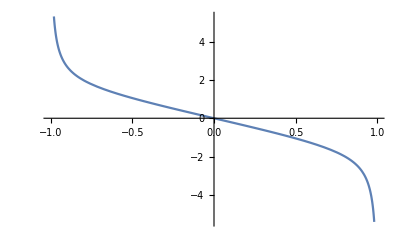

```mathematica
Plot[ LegendreQ[1,1,x] , {x,-1,1}]
```

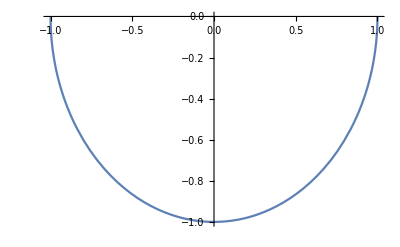

```mathematica
Plot[ LegendreP[1,1,x] , {x,-1,1}]
```

```mathematica
(* osservo che il LegendreQ divergono e LegendreP sono convergenti in {x,-1,1} ; escludo i primi annullando la costante arbitraria*)
```

```mathematica
eq2= -D[TH[th] PHI[phi] , {phi,2}] ==m^2 TH[th] PHI[phi];
sol2 = DSolve[ eq2 , PHI[phi], phi];
sol2 = sol2 /. {C[1]->1 , C[2]->I};
sol22= D[ sol2, {phi,2}];

eq1= -1/Sin[th] D[ Sin[th] D[ TH[th] PHI[phi], th] , th] - 1/Sin[th]^2 D[ TH[th] PHI[phi] , {phi,2}] == l(l+1) TH[th] PHI[phi];

eq1 = eq1 /.sol2 /.sol22;

sol1=DSolve[ eq1 , TH[th], th];
sol1= sol1 /. {C[1] -> 1, C[2]-> 0};

Psi[th_, phi_, l_, m_] = TH[th] PHI[phi] /.sol1 /.sol2;
Psi2[th_, phi_, l_, m_] := TH[th] PHI[phi] /.sol1 /.sol2;
```

```mathematica
Psi2[a,b,c,d]
```

{{PHI[b] TH[a]}}

```mathematica
(* il := ha un comportamento anomalo chiamato con [a,b,c,d], perchè sol1 e sol2 sono funz di TH[th] e PHI[phi] non di Th[a] e di PHI[b] e Mathematica non riesce a valutare, va alla ricerca dell'espressione uguale identica *)
```

```mathematica
ParametricPlot3D[{Sin[th] Sin[phi] , Sin[th] Cos[phi], Cos[th] }, {th,0,Pi} , {phi , 0 ,2 Pi}]
```

-Graphics3D-

```mathematica
eq2= -D[TH[th] PHI[phi] , {phi,2}] ==m^2 TH[th] PHI[phi];
sol2 = DSolve[ eq2 , PHI[phi], phi];
sol2 = sol2 /. {C[1]->1 , C[2]->I};
sol22= D[ sol2, {phi,2}];

eq1= -1/Sin[th] D[ Sin[th] D[ TH[th] PHI[phi], th] , th] - 1/Sin[th]^2 D[ TH[th] PHI[phi] , {phi,2}] == l(l+1) TH[th] PHI[phi];

eq1 = eq1 /.sol2 /.sol22;

sol1=DSolve[ eq1 , TH[th], th];
sol1= sol1 /. {C[1] -> 1, C[2]-> 0};

Psi[th_, phi_, l_, m_] = TH[th] PHI[phi] /.sol1 /.sol2;
grafico[l_, m_]:=ParametricPlot3D[ r=Abs[ Psi[ th,phi,l,m]];
                      {r Sin[th] Sin[phi] , r Sin[th] Cos[phi] ,r Cos[th]}, {th, 0, Pi}, {phi, 0,Pi} ];
```

```mathematica
grafico[1,1]
```

-Graphics3D-

```mathematica
eq2= -D[TH[th] PHI[phi] , {phi,2}] ==m^2 TH[th] PHI[phi];
sol2 = DSolve[ eq2 , PHI[phi], phi][[1]];
sol2 = sol2 /. {C[1]->1 , C[2]->I};
sol22= D[ sol2, {phi,2}];

eq1= -1/Sin[th] D[ Sin[th] D[ TH[th] PHI[phi], th] , th] - 1/Sin[th]^2 D[ TH[th] PHI[phi] , {phi,2}] == l(l+1) TH[th] PHI[phi];

eq1 = eq1 /.sol2 /.sol22;

sol1=DSolve[ eq1 , TH[th], th][[1]];
sol1= sol1 /. {C[1] -> 1, C[2]-> 0};

Psi[th_, phi_, l_, m_] := TH[th] PHI[phi] /.sol1 /.sol2;
grafico[l_, m_]:=ParametricPlot3D[
                                                                         r=Abs[ Psi[th,phi,l,m]]; {r Sin[th] Sin[phi],r  Sin[th] Cos[phi], r Cos[th] },
 {th,0,Pi} , {phi , 0 ,Pi}
                                                                        ];

(* 

x=Cos[th];
d/dth diventa dx/dth d/dx = -Sqrt[1-x^2] d/dx 

*)
(* f_ --> su qualunque funzione *)

Derivative[1][f_][th]:= -Sqrt[1-x^2]f'[x];
Derivative[n_][f_][th] := -Sqrt[1-x^2]D[ Derivative[n-1][f][th] , x];

subth = { Cos[th] -> x , Sin[th] ->Sqrt[1-x^2] , Csc[th] -> 1/Sqrt[1-x^2], Cot[th]->x/Sqrt[1-x^2], TH[th]->TH[x] };
```

```mathematica
grafico[1,1]
```

-Graphics3D-